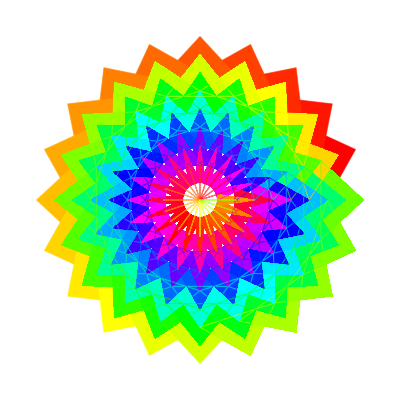

```mathematica
With[
	{d= 2Pi/20},
	Graphics[
	Table[
	{
	EdgeForm[Opacity[.6]],
	Hue[(-11+q+10 r)/72],
	Polygon[
	{
	(8-r) {Cos[d (q-1)],Sin[d (q-1)]},
	(8-r) {Cos[d (q+1)],Sin[d (q+1)]},
	(10-r) {Cos[d q],Sin[d q]}}]
	},
	{r,8},
	{q,20}
]
]
]
```

```mathematica
Animate[
Graphics[
Rotate[
Polygon[
Table[
{Cos[t],Sin[t]},
{t,0,4 Pi,4 Pi/5}
]
],
θ,
{0,0}
],PlotRange->1.2],{θ,0,2 π},AnimationRunning->False]
```

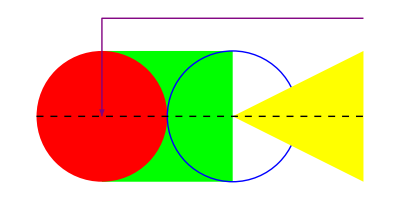

```mathematica
Graphics[{
Thick,Green,Rectangle[{0,-1},{2,1}],
Red,Disk[],
Blue,Circle[{2,0}],
Yellow,Polygon[{{2,0},{4,1},{4,-1}}],
Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]
}]
```

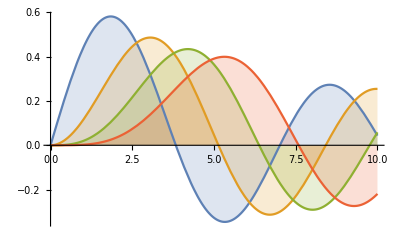

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

```mathematica
GraphPlot[Table[i->Mod[i^2,102],{i,0,102}] ,PlotTheme->"Minimal"]
```

-Graphics-

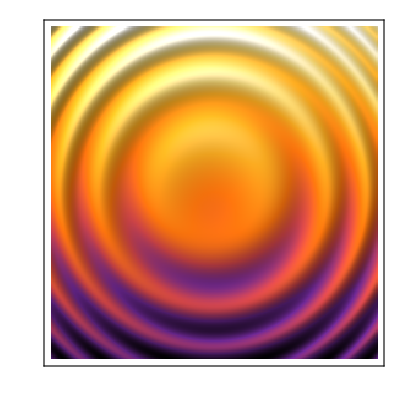

```mathematica
ReliefPlot[Table[i+Sin[i^2+j^2],{i,-4,4,.03},{j,-4,4,.03}],ColorFunction->"SunsetColors"]
```

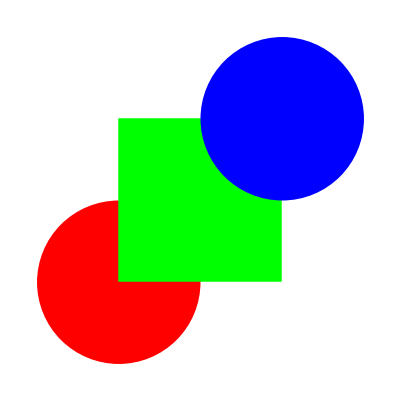

```mathematica
Graphics[{Red,Disk[],Green,Rectangle[{0,0},{2,2}],Blue,Disk[{2,2}]}]
```

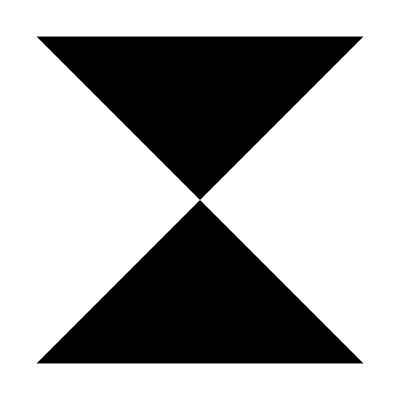

```mathematica
Graphics[Polygon[{{0,0},{1,1},{0,1},{1,0}}]]
```

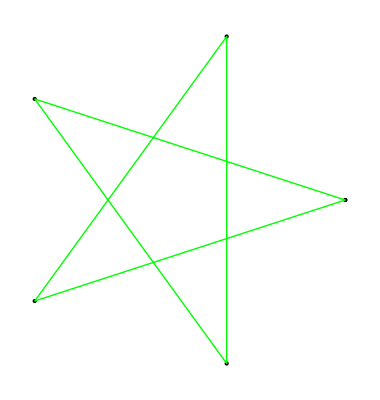

```mathematica
v=Table[15 {Cos[t],Sin[t]},{t,0,4 Pi,4 Pi/5}];
Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Green,Line[{1,2,3,4,5,6}]}]]
```

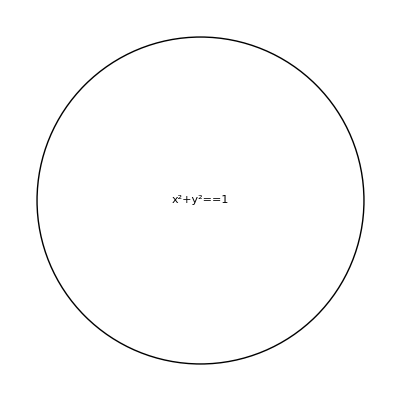

```mathematica
Graphics[{Circle[],Inset[x^2+y^2==1,{0,0}]}]
```

```mathematica
{Graphics[{Red,Disk[]}],Graphics[{Green,Disk[],Yellow,Opacity[.7],Disk[{0,1}]}],Graphics[{Hue[2/3,1/2,1],Rectangle[]}]}
```


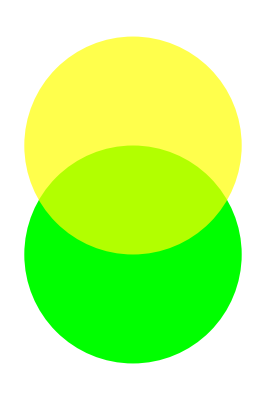

```mathematica
Table[Graphics[{Inset[Graphics[Circle[],ImageSize->30,AlignmentPoint->{0,a}],Center]},ImageSize->70,Axes->True,Ticks->None],{a,{-1,0,1}}]
```

{-Graphics-,-Graphics-,-Graphics-}

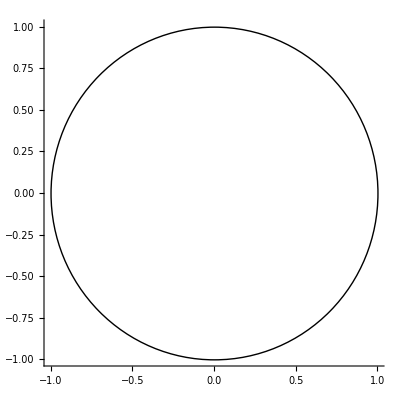

```mathematica
Graphics[Circle[],Axes->True,AxesStyle->{Directive[Dashed,Red],Blue}]
```

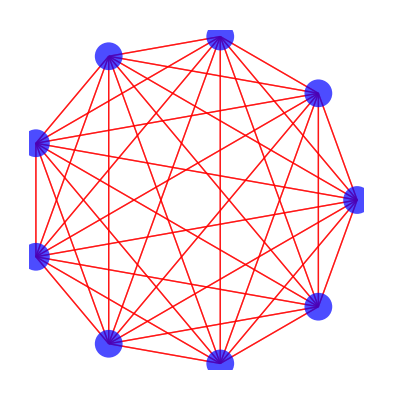

```mathematica
pts=Table[{Cos[2 n π/9],Sin[2 n π/9]},{n,0,8}];
Graphics[{Opacity[0.7],Red,Line[Tuples[pts,2]],Blue,PointSize[0.05],Point[pts]}]
```

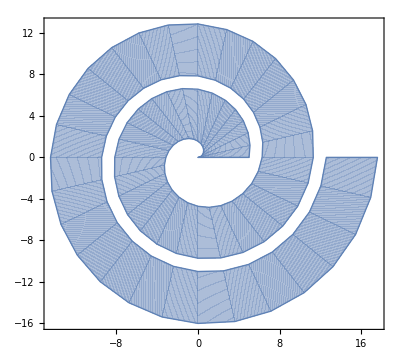

```mathematica
ParametricPlot[{(v+u) Cos[u],(v+u) Sin[u]},{u,0,4 Pi},{v,0,5},Mesh->False]
```

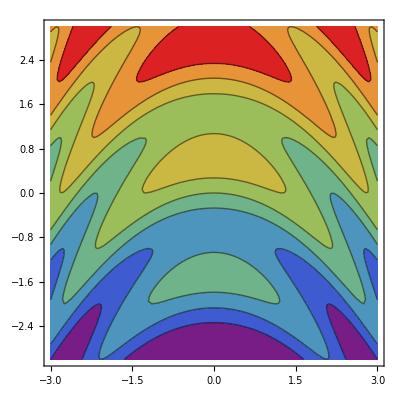

```mathematica
ContourPlot[y+Sin[x^2+3 y],{x,-3,3},{y,-3,3},ColorFunction->"Rainbow"]
```

```mathematica
Dynamic@Module[{hour,min,sec,ht,mt,st},Clock[];{hour,min,sec}=Take[DateList[],-3];
ht=Pi/2-2 Pi hour/12-2 Pi min/720;mt=Pi/2-2 Pi min/60;
st=Pi/2-2 Pi Floor[sec]/60;
Graphics[{Arrowheads[0.1],Arrow[{{0,0},0.6 {Cos[ht],Sin[ht]}}],Arrow[{{0,0},0.85 {Cos[mt],Sin[mt]}}],Line[{{0,0},0.85 {Cos[st],Sin[st]}}],PointSize[Medium],Table[Point[0.9 {Cos[i],Sin[i]}],{i,0,2 Pi,Pi/6}],Point[{0,0}],Circle[]}]]
```

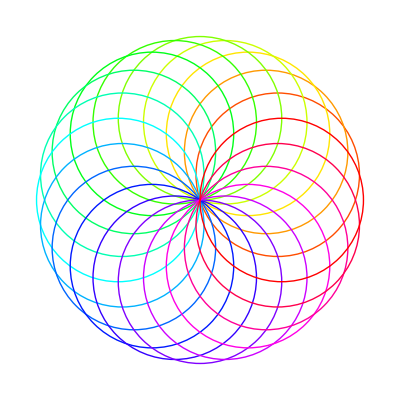

```mathematica
Graphics[Table[{Hue[t/20],Circle[{Cos[2 Pi t/20],Sin[2 Pi t/20]}]},{t,20}]]
```